## Holling

### Holling type III

```mathematica
Series[(aij yj^k)/(1+ aij hij yj^k),{hij,0,2}]
```

aij yj^k-aij^2 yj^(2 k) hij+aij^3 yj^(3 k) hij^2+O[hij]^3

### We will be focusing on Holling type II

```mathematica
Series[(aij yj)/(1+ aij hij yj),{hij,0,2}]
```

aij yj-aij^2 yj^2 hij+aij^3 yj^3 hij^2+O[hij]^3

```mathematica
a={{3.15,0.6},{2.5,2.9}};
h={{-0.135,-1.5},{-0.1,-0.23}};
r1=0.1;r2=0.25;
```

```mathematica
n=2;
```

```mathematica
{Subscript[y, 1]'[t]==Subscript[y, 1][t](r1+∑_(j=1)^n (a⟦1,j⟧ Subscript[y, j][t]+a⟦1,j⟧^2 (Subscript[y, j][t])^2 h⟦1,j⟧)),
Subscript[y, 2]'[t]==Subscript[y, 2][t](r2+∑_(j=1)^n (a⟦2,j⟧ Subscript[y, j][t]+a⟦2,j⟧^2 (Subscript[y, j][t])^2 h⟦2,j⟧))}
```

{y_1'[t]==y_1[t] (0.1+3.15 y_1[t]-1.33954 y_1[t]^2+0.6 y_2[t]-0.54 y_2[t]^2),y_2'[t]==y_2[t] (0.25+2.5 y_1[t]-0.625 y_1[t]^2+2.9 y_2[t]-1.9343 y_2[t]^2)}

```mathematica
int={y1,y2}/.Solve[{y1 (r1+a⟦1,1⟧ y1+a⟦1,1⟧^2 h⟦1,1⟧ y1^2+a⟦1,2⟧ y2+a⟦1,2⟧^2 h⟦1,2⟧ y2^2)==0&&
y2 (r2+a⟦2,1⟧ y1+a⟦2,1⟧^2 h⟦2,1⟧ y1^2+a⟦2,2⟧ y2+a⟦2,2⟧^2 h⟦2,2⟧ y2^2)==0},{y1,y2},Assumptions->{y1>0&&y2>0}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
predprey=NDSolve[{
Subscript[y, 1]'[t]==Subscript[y, 1][t](r1+∑_(j=1)^n (a⟦1,j⟧ Subscript[y, j][t]+a⟦1,j⟧^2 (Subscript[y, j][t])^2 h⟦1,j⟧)),
Subscript[y, 2]'[t]==Subscript[y, 2][t](r2+∑_(j=1)^n (a⟦2,j⟧ Subscript[y, j][t]+a⟦2,j⟧^2 (Subscript[y, j][t])^2 h⟦2,j⟧)),
Subscript[y, 1][0]==0.5,Subscript[y, 2][0]==0.5},{Subscript[y, 1],Subscript[y, 2]},{t,0,5,0.1}]
```

{{y_1→InterpolatingFunction[…],y_2→InterpolatingFunction[…]}}

```mathematica
trajectory=ListPlot[Table[Evaluate[{Subscript[y, 1][t],Subscript[y, 2][t]}/.predprey]⟦1⟧,{t,0,5,0.005}],Joined->True,Axes->None,PlotStyle->Black,PlotStyle->Black,PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],PlotRange->{{-0.5,3},{-0.5,3}},FrameLabel->{Style["Species 1",16,RGBColor["#807FFF"]],Style["Species 2",16,RGBColor["#DEAD26"]]},AspectRatio->1,Epilog->{Red,PointSize[Medium],Point[int]}];
```

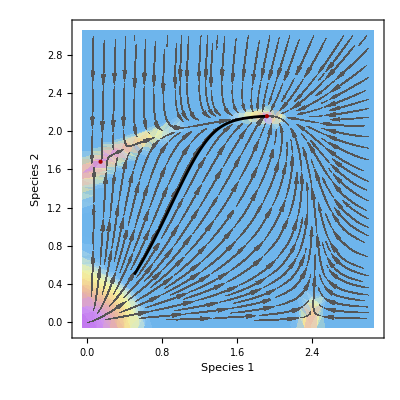

```mathematica
Show[StreamDensityPlot[{y1 (r1+a⟦1,1⟧ y1+a⟦1,1⟧^2 h⟦1,1⟧ y1^2+a⟦1,2⟧ y2+a⟦1,2⟧^2 h⟦1,2⟧ y2^2),
y2 (r2+a⟦2,1⟧ y1+a⟦2,1⟧^2 h⟦2,1⟧ y1^2+a⟦2,2⟧ y2+a⟦2,2⟧^2 h⟦2,2⟧ y2^2)},{y1,0,3},{y2,0,3},Frame->True,ColorFunction->"Pastel",ColorFunctionScaling->False,StreamStyle->Darker[Gray],StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,FrameLabel->{Style["Species 1",16,RGBColor["#807FFF"]],Style["Species 2",16,RGBColor["#DEAD26"]]},AspectRatio->1,PlotRange->{{-0.1,3.1},{-0.1,3.1}}],trajectory,Epilog->{Darker[Red],PointSize[Large],Point[int]},FrameStyle->Directive[Black,Thickness[0.004]]]
```

### Using the notation as used in the manuscript

```mathematica
c=.;
bigc=Table[Subscript[c, i,j,k],{i,1,2},{j,1,2},{k,1,2}];
```

```mathematica
Subscript[c, 1,1,1]=h⟦1,1⟧ a⟦1,1⟧^2;Subscript[c, 1,1,2]=0;
Subscript[c, 1,2,2]=h⟦1,2⟧ a⟦1,2⟧^2;Subscript[c, 1,2,1]=0;
```

```mathematica
Subscript[c, 2,1,1]=h⟦2,1⟧ a⟦2,1⟧^2;Subscript[c, 2,1,2]=0;
Subscript[c, 2,2,2]=h⟦2,2⟧ a⟦2,2⟧^2;Subscript[c, 2,2,1]=0;
```

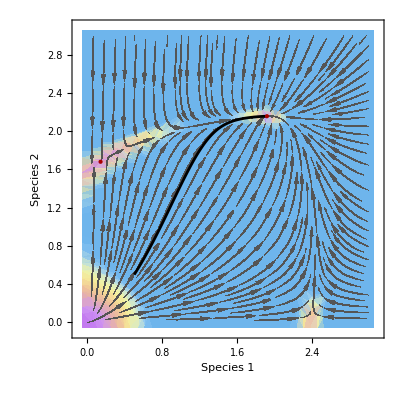

```mathematica
Show[StreamDensityPlot[{y1 (r1+a⟦1,1⟧ y1+a⟦1,2⟧ y2 + Subscript[c, 1,1,1] y1 y1 +Subscript[c, 1,1,2] y1 y2 +Subscript[c, 1,2,1] y2 y1 +Subscript[c, 1,2,2] y2 y2 ),
y2 (r2+a⟦2,1⟧ y1+a⟦2,2⟧ y2 + Subscript[c, 2,1,1] y1 y1 +Subscript[c, 2,1,2] y1 y2 +Subscript[c, 2,2,1] y2 y1 +Subscript[c, 2,2,2] y2 y2)},{y1,0,3},{y2,0,3},Frame->True,ColorFunction->"Pastel",ColorFunctionScaling->False,StreamStyle->Darker[Gray],StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,FrameLabel->{Style["Species 1",16,RGBColor["#807FFF"]],Style["Species 2",16,RGBColor["#DEAD26"]]},AspectRatio->1,PlotRange->{{-0.1,3.1},{-0.1,3.1}}],trajectory,Epilog->{Darker[Red],PointSize[Large],Point[int]},FrameStyle->Directive[Black,Thickness[0.004]]]
```

### Converting to Replicator

LV equations using the replicator matrix look like

```mathematica
m=3;
(*Table[Subscript[b, i,j,k]=.,{i,1,m},{j,1,m},{k,1,m}]*)
Table[Subscript[y, i]'[t]==Subscript[y, i][t] ((Subscript[b, i,m,m]-Subscript[b, m,m,m])+∑_(j=1)^n (Subscript[b, i,j,m]-Subscript[b, m,j,m])Subscript[y, j][t]+∑_(k=1)^n (Subscript[b, i,m,k]-Subscript[b, m,m,k])Subscript[y, k][t]+(∑_(j=1)^n ∑_(k=1)^n (Subscript[b, i,j,k]-Subscript[b, m,j,k])Subscript[y, j][t]Subscript[y, k][t])),{i,1,2,1}]
```

{y_1'[t]==y_1[t] (b_(1,3,3)-b_(3,3,3)+(b_(1,1,3)-b_(3,1,3)) y_1[t]+(b_(1,3,1)-b_(3,3,1)) y_1[t]+(b_(1,1,1)-b_(3,1,1)) y_1[t]^2+(b_(1,2,3)-b_(3,2,3)) y_2[t]+(b_(1,3,2)-b_(3,3,2)) y_2[t]+(b_(1,1,2)-b_(3,1,2)) y_1[t] y_2[t]+(b_(1,2,1)-b_(3,2,1)) y_1[t] y_2[t]+(b_(1,2,2)-b_(3,2,2)) y_2[t]^2),y_2'[t]==y_2[t] (b_(2,3,3)-b_(3,3,3)+(b_(2,1,3)-b_(3,1,3)) y_1[t]+(b_(2,3,1)-b_(3,3,1)) y_1[t]+(b_(2,1,1)-b_(3,1,1)) y_1[t]^2+(b_(2,2,3)-b_(3,2,3)) y_2[t]+(b_(2,3,2)-b_(3,3,2)) y_2[t]+(b_(2,1,2)-b_(3,1,2)) y_1[t] y_2[t]+(b_(2,2,1)-b_(3,2,1)) y_1[t] y_2[t]+(b_(2,2,2)-b_(3,2,2)) y_2[t]^2)}

```mathematica
coeff1=CoefficientList[Simplify[(Subscript[b, 1,3,3]-Subscript[b, 3,3,3]+(Subscript[b, 1,1,3]-Subscript[b, 3,1,3]) y1+(Subscript[b, 1,3,1]-Subscript[b, 3,3,1]) y1+(Subscript[b, 1,1,1]-Subscript[b, 3,1,1]) y1^2+(Subscript[b, 1,2,3]-Subscript[b, 3,2,3]) y2+(Subscript[b, 1,3,2]-Subscript[b, 3,3,2]) y2+(Subscript[b, 1,1,2]-Subscript[b, 3,1,2]) y1 y2+(Subscript[b, 1,2,1]-Subscript[b, 3,2,1]) y1 y2+(Subscript[b, 1,2,2]-Subscript[b, 3,2,2]) y2^2)],{y1,y2}]//Simplify;
```

```mathematica
coeff1rhs=CoefficientList[(r1+a⟦1,1⟧ y1+a⟦1,2⟧ y2 + Subscript[c, 1,1,1] y1 y1 +Subscript[c, 1,1,2] y1 y2 +Subscript[c, 1,2,1] y2 y1 +Subscript[c, 1,2,2] y2 y2 ),{y1,y2}];
```

```mathematica
coeff2=CoefficientList[Simplify[(Subscript[b, 2,3,3]-Subscript[b, 3,3,3]+(Subscript[b, 2,1,3]-Subscript[b, 3,1,3]) y1+(Subscript[b, 2,3,1]-Subscript[b, 3,3,1]) y1+(Subscript[b, 2,1,1]-Subscript[b, 3,1,1]) y1^2+(Subscript[b, 2,2,3]-Subscript[b, 3,2,3]) y2+(Subscript[b, 2,3,2]-Subscript[b, 3,3,2]) y2+(Subscript[b, 2,1,2]-Subscript[b, 3,1,2]) y1 y2+(Subscript[b, 2,2,1]-Subscript[b, 3,2,1]) y1 y2+(Subscript[b, 2,2,2]-Subscript[b, 3,2,2]) y2^2)],{y1,y2}];
```

```mathematica
coeff2rhs=CoefficientList[(r2+a⟦2,1⟧ y1+a⟦2,2⟧ y2 + Subscript[c, 2,1,1] y1 y1 +Subscript[c, 2,1,2] y1 y2 +Subscript[c, 2,2,1] y2 y1 +Subscript[c, 2,2,2] y2 y2),{y1,y2}];
```

Let  us  fill the last strategy to be 0s

```mathematica
Table[Subscript[b, m,i,j]=0,{i,1,m},{j,1,m}];
```

```mathematica
coeff1
```

{{b_(1,3,3),b_(1,2,3)+b_(1,3,2),b_(1,2,2)},{b_(1,1,3)+b_(1,3,1),b_(1,1,2)+b_(1,2,1),0},{b_(1,1,1),0,0}}

```mathematica
coeff1rhs
```

{{0.1,0.6,-0.54},{3.15,0,0},{-1.33954,0,0}}

```mathematica
Subscript[b, 1,3,3]=coeff1rhs⟦1,1⟧;Subscript[b, 1,2,3]=coeff1rhs⟦1,2⟧;Subscript[b, 1,3,2]=0;Subscript[b, 1,2,2]=coeff1rhs⟦1,3⟧;
Subscript[b, 1,1,3]=coeff1rhs⟦2,1⟧;Subscript[b, 1,3,1]=0;Subscript[b, 1,1,2]=coeff1rhs⟦2,2⟧;Subscript[b, 1,2,1]=0;Subscript[b, 1,1,1]=coeff1rhs⟦3,1⟧;
```

```mathematica
coeff2
```

{{b_(2,3,3),b_(2,2,3)+b_(2,3,2),b_(2,2,2)},{b_(2,1,3)+b_(2,3,1),b_(2,1,2)+b_(2,2,1),0},{b_(2,1,1),0,0}}

```mathematica
coeff2rhs
```

{{0.25,2.9,-1.9343},{2.5,0,0},{-0.625,0,0}}

```mathematica
Subscript[b, 2,3,3]=coeff2rhs⟦1,1⟧;Subscript[b, 2,2,3]=coeff2rhs⟦1,2⟧;Subscript[b, 2,3,2]=0;Subscript[b, 2,2,2]=coeff2rhs⟦1,3⟧;
Subscript[b, 2,1,3]=coeff2rhs⟦2,1⟧;Subscript[b, 2,3,1]=0;Subscript[b, 2,1,2]=coeff2rhs⟦2,2⟧;Subscript[b, 2,2,1]=0;Subscript[b, 2,1,1]=coeff2rhs⟦3,1⟧;
```

```mathematica
B=Table[Subscript[b, i,j,k],{i,1,m},{j,1,m},{k,1,m}]
```

{{{-1.33954,0,3.15},{0,-0.54,0.6},{0,0,0.1}},{{-0.625,0,2.5},{0,-1.9343,2.9},{0,0,0.25}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
B//MatrixForm
```

((-1.33954
0
3.15) | (0
-0.54
0.6) | (0
0
0.1)
(-0.625
0
2.5) | (0
-1.9343
2.9) | (0
0
0.25)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
{{Subscript[b, 1,1,1],Subscript[b, 1,1,2],Subscript[b, 1,1,3],Subscript[b, 1,2,1],Subscript[b, 1,2,2],Subscript[b, 1,2,3],Subscript[b, 1,3,1],Subscript[b, 1,3,2],Subscript[b, 1,3,3]},
{Subscript[b, 2,1,1],Subscript[b, 2,1,2],Subscript[b, 2,1,3],Subscript[b, 2,2,1],Subscript[b, 2,2,2],Subscript[b, 2,2,3],Subscript[b, 2,3,1],Subscript[b, 2,3,2],Subscript[b, 2,3,3]},
{Subscript[b, 3,1,1],Subscript[b, 3,1,2],Subscript[b, 3,1,3],Subscript[b, 3,2,1],Subscript[b, 3,2,2],Subscript[b, 3,2,3],Subscript[b, 3,3,1],Subscript[b, 3,3,2],Subscript[b, 3,3,3]}}//MatrixForm
```

(-1.33954 | 0 | 3.15 | 0 | -0.54 | 0.6 | 0 | 0 | 0.1
-0.625 | 0 | 2.5 | 0 | -1.9343 | 2.9 | 0 | 0 | 0.25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TeXForm[%]
```

\left(
\begin{array}{ccccccccc}
 -1.33954 & 0 & 3.15 & 0 & -0.54 & 0.6 & 0 & 0 & 0.1 \\
 -0.625 & 0 & 2.5 & 0 & -1.9343 & 2.9 & 0 & 0 & 0.25 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

Plotting  the game dynamics

### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

```mathematica
payoffs=B;
fits[x_,y_]:=Table[∑_(j=1)^3 (∑_(k=1)^3 (payoffs⟦i,j,k⟧ Subscript[x, j] Subscript[x, k])),{i,1,3}]/.{Subscript[x, 1]->x,Subscript[x, 2]->y,Subscript[x, 3]->1-x-y};
```

```mathematica
π1[x_,y_,z_]:=fits[x,y]⟦1⟧;

π2[x_,y_,z_]:=fits[x,y]⟦2⟧;

π3[x_,y_,z_]:=fits[x,y]⟦3⟧;
πbar[x_,y_,z_]:=x π1[x,y,z]+y π2[x,y,z]+z π3[x,y,z];
dx[x_, y_, z_]:=x(π1[x,y,z]-πbar[x,y,z]);
dy[x_, y_, z_]:=y(π2[x,y,z]-πbar[x,y,z]);
dz[x_, y_, z_]:=z(π3[x,y,z]-πbar[x,y,z]);

Fermi[x_]:={
dx[x⟦1⟧,x⟦2⟧, x⟦3⟧],
dy[x⟦1⟧,x⟦2⟧, x⟦3⟧],
dz[x⟦1⟧,x⟦2⟧, x⟦3⟧]
}
x=.;y=.;z=1-x-y;
fa=fits[x,y]⟦1⟧;
fb=fits[x,y]⟦2⟧;
fc=fits[x,y]⟦3⟧;
```

```mathematica
x=.
y=.
sol=NSolve[{dx[x,y,1-x-y]==0,dy[x,y,1-x-y]==0},{x,y},NonNegativeReals];
```

```mathematica
data={x,y}/.sol;
relData=Select[data,Total[#]<=1&&Total[#]≥0&];
p1=ListPlot[relData,PlotStyle->{Black,PointSize[0.025]}];
p2=ListPlot[relData,PlotStyle->{White,PointSize[0.015]}];
p3=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{Red,PointSize[0.03]}];
p4=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{White,PointSize[0.015]}];
points=Show[p1,p2,p3,p4];
```

Plotting  isoclines

```mathematica
eq1=fa-fc;
eq2=fb-fc;
```

```mathematica
cplt=ContourPlot[eq1==0,{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y≤1],PlotRange->All,ContourStyle->Darker[Red]];
cplt2=ContourPlot[eq2==0,{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y≤1],PlotRange->All,ContourStyle->Darker[Blue]];
```

```mathematica
sp=StreamDensityPlot[{dx[x,y,1-x-y],dy[x,y,1-x-y]},{x,0,1},{y,0,1},Frame->True,ColorFunction->"Pastel",ColorFunctionScaling->False,StreamStyle->Darker[Gray],StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,RegionFunction->Function[{x,y,vx,vy,n},x +y≤1&&x≥0&&y≥0]];
```

```mathematica
trajdata=NDSolve[{x'[t]==dx[x[t],y[t],1-x[t]-y[t]],y'[t]==dy[x[t],y[t],1-x[t]-y[t]],x[0]==0.45,y[0]==0.08},{x,y},{t,0,50}];
parpl=ParametricPlot[Evaluate[{x[t],y[t]}/.trajdata],{t,0,50},PlotRange->All,PlotStyle->Directive[Black,Dashed]];
```

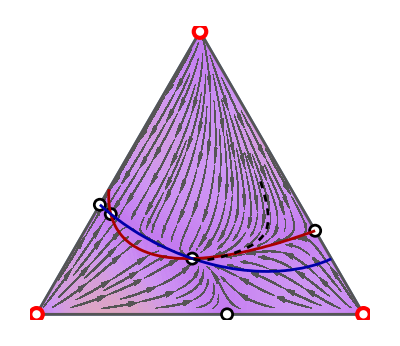

```mathematica
psim=Show[
Graphics[GeometricTransformation[First[Show[sp]],trans]],triangle,Graphics[GeometricTransformation[First[Show[points]],trans]],
Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],
Graphics[GeometricTransformation[First[parpl],trans]](*,
Graphics[GeometricTransformation[Text["label",{0,1}],trans]]*)
]
```